```mathematica
dataset=Import["/Volumes/UDISK/temp","Table"];
```

```mathematica
dataset2=Split[Sort[dataset,#1[[3]]<#2[[3]]&],#2[[3]]==#1[[3]]&];
```

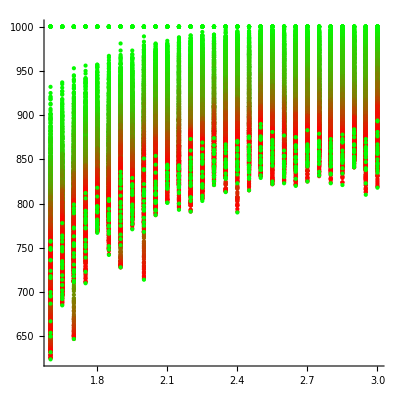

```mathematica
ListPlot[dataset2[[All,All,{2,1}]],PlotStyle->Table[RGBColor[i/100,1-i/100,0],{i,100}],AspectRatio->1]
```

```mathematica
Graphics[Rectangle[{0,0},{0.1,0.01}],ImageSize->15]
```

-Graphics-